# Load Full Dataset

```mathematica
SetDirectory[NotebookDirectory[]];
{rawBuildings,rawHabitats}={Import["./data/Machabuildings.csv"],Import["./data/ChomaAQHB.csv"]};
{buildingsCoords,habitatsCoords}=(#[[2;;All,2;;All]])&/@{rawBuildings,rawHabitats};
```

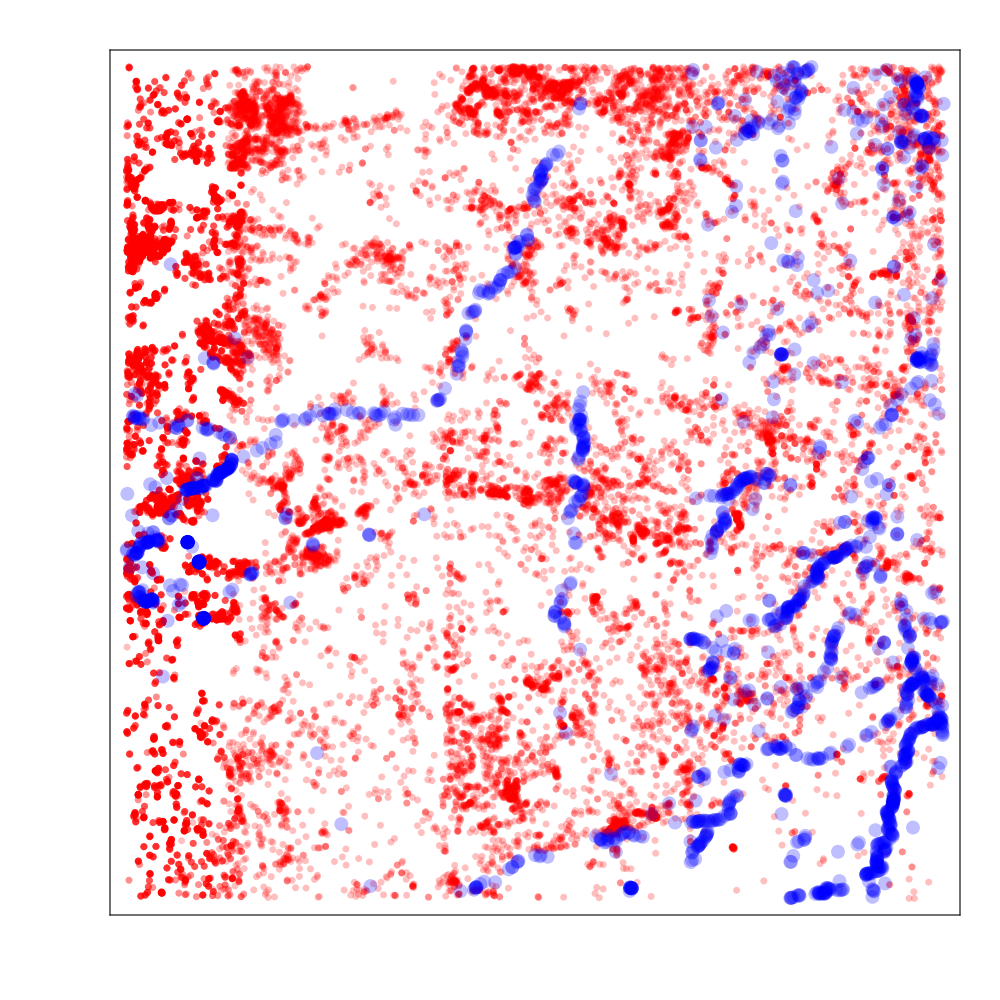

```mathematica
ListPlot[{buildingsCoords,habitatsCoords}
,AspectRatio->1
,Frame->True
,FrameStyle->Directive[Black,Opacity[.5],Thickness[.01]]
,FrameTicks->None
,PlotRangePadding->0
,ImageSize->1000
,PlotStyle->{Directive[Opacity[.25],PointSize[.005],Red],Directive[Opacity[.25],PointSize[.01],Blue]}
]
```